{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

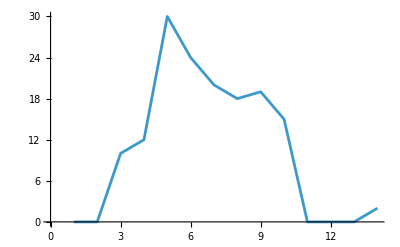

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt12=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{2,4}]
```

ContinuousWaveletData[…]

```mathematica
cwt14=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{4,4}]
```

ContinuousWaveletData[…]

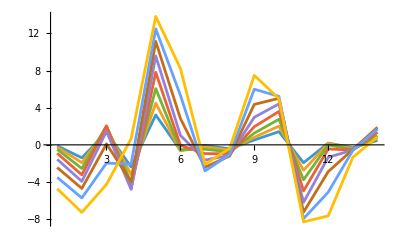

```mathematica
ListLinePlot[cwt12[All,"Values"]//Re,PlotRange->Full]
```

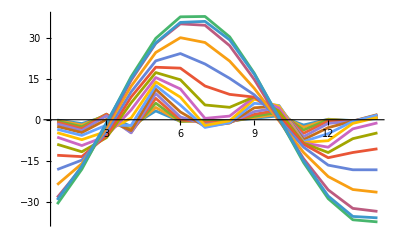

```mathematica
ListLinePlot[cwt14[All,"Values"]//Re,PlotRange->Full]
```

```mathematica
cwt12[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

```mathematica
cwt14[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

{0,0,10,12,30,40,60,100,110,111}

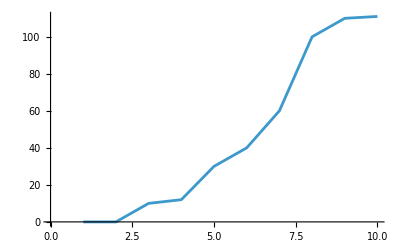

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

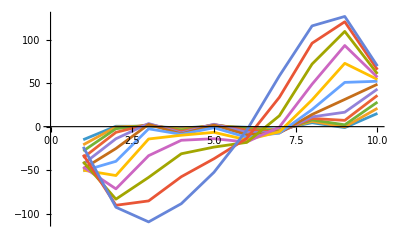

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.224447,0.880949,0.209664,0.0345492,0.753413,0.0111973,0.53767,0.994487,0.497751,0.0404329}

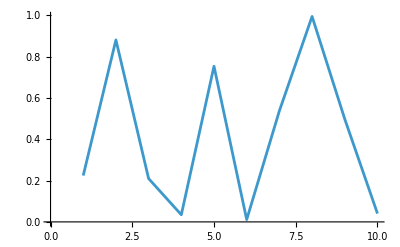

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

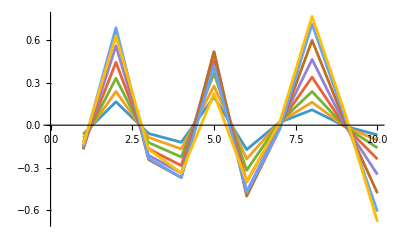

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

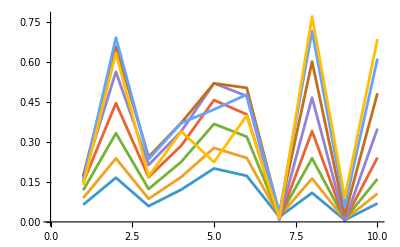

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

ピーク推定

モジュール読み込み：

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txt"]
```

Get::noopen: /Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txtを開くことができません．

$Failed

```mathematica
cwtr[All,"Values"]
```

{{-0.0643496,0.165418,-0.0590591,-0.120902,0.200085,-0.172482,0.018731,0.108756,-0.00711576,-0.0690821},{-0.0892377,0.237791,-0.0864662,-0.16822,0.276911,-0.239461,0.021053,0.162329,-0.00887357,-0.105826},{-0.11832+0. ⅈ,0.331917-1.11022×10^-17 ⅈ,-0.123082-1.05588×10^-17 ⅈ,-0.22505-3.43078×10^-18 ⅈ,0.366651-6.52573×10^-18 ⅈ,-0.319081+8.98189×10^-18 ⅈ,0.0191578+6.52573×10^-18 ⅈ,0.238028+8.98189×10^-18 ⅈ,-0.00942543+1.05588×10^-17 ⅈ,-0.160794-3.43078×10^-18 ⅈ},{-0.147265,0.444485,-0.167643,-0.285783,0.456098,-0.402201,0.00959258,0.339604,-0.00643274,-0.240454},{-0.168033,0.561809,-0.213139,-0.339336,0.519077,-0.470984,-0.00914503,0.465019,0.00388606,-0.349154},{-0.171548,0.656126,-0.243429,-0.371129,0.518485,-0.501841,-0.0305038,0.600124,0.0253594,-0.481643},{-0.156348,0.689719,-0.234825,-0.370215,0.420844,-0.476698,-0.0331903,0.714528,0.0573779,-0.611193},{-0.138139,0.632693,-0.170758,-0.338725,0.223789,-0.398019,0.0142965,0.769033,0.0900151,-0.684186}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

WTPE[{{-0.0643496,0.165418,-0.0590591,-0.120902,0.200085,-0.172482,0.018731,0.108756,-0.00711576,-0.0690821},{-0.0892377,0.237791,-0.0864662,-0.16822,0.276911,-0.239461,0.021053,0.162329,-0.00887357,-0.105826},{-0.11832+0. ⅈ,0.331917-1.11022×10^-17 ⅈ,-0.123082-1.05588×10^-17 ⅈ,-0.22505-3.43078×10^-18 ⅈ,0.366651-6.52573×10^-18 ⅈ,-0.319081+8.98189×10^-18 ⅈ,0.0191578+6.52573×10^-18 ⅈ,0.238028+8.98189×10^-18 ⅈ,-0.00942543+1.05588×10^-17 ⅈ,-0.160794-3.43078×10^-18 ⅈ},{-0.147265,0.444485,-0.167643,-0.285783,0.456098,-0.402201,0.00959258,0.339604,-0.00643274,-0.240454},{-0.168033,0.561809,-0.213139,-0.339336,0.519077,-0.470984,-0.00914503,0.465019,0.00388606,-0.349154},{-0.171548,0.656126,-0.243429,-0.371129,0.518485,-0.501841,-0.0305038,0.600124,0.0253594,-0.481643},{-0.156348,0.689719,-0.234825,-0.370215,0.420844,-0.476698,-0.0331903,0.714528,0.0573779,-0.611193},{-0.138139,0.632693,-0.170758,-0.338725,0.223789,-0.398019,0.0142965,0.769033,0.0900151,-0.684186}}]

```mathematica
cwt2[All,"Values"]//WTPE
```

WTPE[{{-15.0158+3.50454×10^-16 ⅈ,0.465471+5.37724×10^-16 ⅈ,0.487579-5.97047×10^-16 ⅈ,-1.66076+8.87437×10^-16 ⅈ,0.792816+6.83045×10^-17 ⅈ,-0.676056-1.04168×10^-16 ⅈ,-3.09651-3.49342×10^-16 ⅈ,4.5449+9.3413×10^-16 ⅈ,-1.07434-1.27281×10^-15 ⅈ,15.2327-4.54681×10^-16 ⅈ},{-20.8956+6.03378×10^-16 ⅈ,-0.347541+6.40072×10^-16 ⅈ,0.988663-1.3247×10^-15 ⅈ,-2.57689+9.45196×10^-16 ⅈ,1.25093-1.33082×10^-16 ⅈ,-1.3049-4.96321×10^-16 ⅈ,-4.1019-1.33082×10^-16 ⅈ,6.07088+1.53098×10^-15 ⅈ,-0.237792-1.3247×10^-15 ⅈ,21.1541-3.07744×10^-16 ⅈ},{-28.0068+8.70577×10^-16 ⅈ,-2.38166+5.50508×10^-16 ⅈ,1.79792-2.53548×10^-15 ⅈ,-3.87801+1.3858×10^-15 ⅈ,1.86747+1.24016×10^-15 ⅈ,-2.39254-8.01024×10^-16 ⅈ,-5.16001-1.4629×10^-15 ⅈ,7.74858+1.90204×10^-15 ⅈ,2.12612-8.64898×10^-16 ⅈ,28.2789-2.84785×10^-16 ⅈ},{-35.7707+1.54291×10^-15 ⅈ,-6.55421+5.88715×10^-16 ⅈ,2.84227-3.14853×10^-15 ⅈ,-5.52763+1.84165×10^-15 ⅈ,2.51153+1.42153×10^-15 ⅈ,-4.1049-1.43858×10^-15 ⅈ,-6.11225-1.28154×10^-15 ⅈ,9.45007+2.61601×10^-15 ⅈ,7.25399-1.47795×10^-15 ⅈ,36.0119-6.64224×10^-16 ⅈ},{-43.0666+2.30119×10^-15 ⅈ,-13.9206+1.85714×10^-16 ⅈ,3.58798-2.84035×10^-15 ⅈ,-7.23467+2.49899×10^-15 ⅈ,2.76196+3.37294×10^-16 ⅈ,-6.48556-2.27186×10^-15 ⅈ,-6.82049+3.37294×10^-16 ⅈ,11.2725+3.13427×10^-15 ⅈ,16.6355-2.84035×10^-15 ⅈ,43.2701-8.4218×10^-16 ⅈ},{-48.4743+2.441×10^-15 ⅈ,-25.1683-3.09376×10^-16 ⅈ,2.62006-1.349×10^-15 ⅈ,-8.43493+2.64659×10^-15 ⅈ,1.82042+1.31241×10^-15 ⅈ,-9.3319-2.52147×10^-15 ⅈ,-7.25895-3.5818×10^-16 ⅈ,14.033+2.88466×10^-15 ⅈ,31.3438-4.05206×10^-15 ⅈ,48.851-6.94579×10^-16 ⅈ},{-50.8974+2.62252×10^-15 ⅈ,-39.891-6.68523×10^-16 ⅈ,-2.46578-2.51902×10^-15 ⅈ,-8.84857+2.60879×10^-15 ⅈ,-1.19825+6.58624×10^-16 ⅈ,-12.2864-2.75787×10^-15 ⅈ,-7.3152+6.58624×10^-16 ⅈ,19.6924+2.64826×10^-15 ⅈ,50.9538-2.51902×10^-15 ⅈ,52.2564-7.32379×10^-16 ⅈ},{-50.0968+2.76385×10^-15 ⅈ,-56.2547+6.11228×10^-16 ⅈ,-14.1775-2.37769×10^-15 ⅈ,-9.8851+2.98836×10^-15 ⅈ,-6.55583+7.99959×10^-16 ⅈ,-15.1731-5.16313×10^-15 ⅈ,-5.96285+7.99959×10^-16 ⅈ,30.857+5.64913×10^-15 ⅈ,72.8983-2.37769×10^-15 ⅈ,54.3506-3.69398×10^-15 ⅈ},{-46.4688+2.82695×10^-15 ⅈ,-71.592+1.43631×10^-15 ⅈ,-33.3888-1.63882×10^-15 ⅈ,-15.6731-1.13446×10^-15 ⅈ,-13.8466+1.2807×10^-15 ⅈ,-17.715+4.54365×10^-16 ⅈ,-0.458425+4.45407×10^-16 ⅈ,48.8893+4.54365×10^-16 ⅈ,93.4056-2.99036×10^-15 ⅈ,56.8478-1.13446×10^-15 ⅈ},{-40.3769,-83.4683,-58.3794,-31.1964,-23.5101,-18.1138,12.5713,72.0706,109.633,60.7704},{-32.2053,-90.4994,-85.47,-57.6367,-36.9133,-13.5188,33.8411,96.0703,120.746,65.5861},{-23.2367-1.35529×10^-22 ⅈ,-92.7565+1.35529×10^-22 ⅈ,-109.632+2.0273×10^-15 ⅈ,-88.663+5.40613×10^-15 ⅈ,-52.4895+1.25294×10^-15 ⅈ,-4.31509+3.34117×10^-15 ⅈ,58.5029-1.25294×10^-15 ⅈ,116.01-3.34117×10^-15 ⅈ,126.855-2.0273×10^-15 ⅈ,69.7251-5.40613×10^-15 ⅈ}}]

```mathematica
cwt[All,"Values"]//WTPE
```

WTPE[cwt[All,Values]]

```mathematica
WTPE[cwt[All,"Values"],"position"]
```

WTPE[cwt[All,Values],position]

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

WTPE[{{-0.0643496,0.165418,-0.0590591,-0.120902,0.200085,-0.172482,0.018731,0.108756,-0.00711576,-0.0690821},{-0.0892377,0.237791,-0.0864662,-0.16822,0.276911,-0.239461,0.021053,0.162329,-0.00887357,-0.105826},{-0.11832+0. ⅈ,0.331917-1.11022×10^-17 ⅈ,-0.123082-1.05588×10^-17 ⅈ,-0.22505-3.43078×10^-18 ⅈ,0.366651-6.52573×10^-18 ⅈ,-0.319081+8.98189×10^-18 ⅈ,0.0191578+6.52573×10^-18 ⅈ,0.238028+8.98189×10^-18 ⅈ,-0.00942543+1.05588×10^-17 ⅈ,-0.160794-3.43078×10^-18 ⅈ},{-0.147265,0.444485,-0.167643,-0.285783,0.456098,-0.402201,0.00959258,0.339604,-0.00643274,-0.240454},{-0.168033,0.561809,-0.213139,-0.339336,0.519077,-0.470984,-0.00914503,0.465019,0.00388606,-0.349154},{-0.171548,0.656126,-0.243429,-0.371129,0.518485,-0.501841,-0.0305038,0.600124,0.0253594,-0.481643},{-0.156348,0.689719,-0.234825,-0.370215,0.420844,-0.476698,-0.0331903,0.714528,0.0573779,-0.611193},{-0.138139,0.632693,-0.170758,-0.338725,0.223789,-0.398019,0.0142965,0.769033,0.0900151,-0.684186}},position]